```mathematica
SetDirectory["D:\\Qsync\\QOLab\\Data\\On Resonance Project\\Lab Book 2 (18 Mar 29 -)\\20-09-28\\Power\\87F11"];
data=Import[#]&/@FileNames["*csv"];
data2=Table[Take[data[[i]],{17,-3}],{i,1,Length[data]}];
SetDirectory["D:\\Qsync\\QOLab\\Data\\On Resonance Project\\Lab Book 2 (18 Mar 29 -)\\20-09-28\\Power\\87F11\\Off"];
dataoff=Import[#]&/@FileNames["*csv"];
data2off=Table[Take[dataoff[[i]],{17,-3}],{i,1,Length[dataoff]}];
```

```mathematica
f[data_]:=Module[{ll,max,min,yaxis1,yaxis2,wcn,ff,gg,loc,kk},
ll=data[[All,2]];
{max,min}=#[ll]&/@{Max,Min};
yaxis1=Take[data[[All,4]],Flatten[{#[ll,min][[1]],#[ll,max][[-1]]}&@Position]];
yaxis2=Take[data[[All,8]],Flatten[{#[ll,min][[1]],#[ll,max][[-1]]}&@Position]];

wcn=(794.76728224*10^-9);


ff[x_]:=Evaluate[Fit[


Flatten[{Table[{o,yaxis1[[o]]},{o,10,200}],Table[{o,yaxis1[[o]]},{o,Length[yaxis1]-200,Length[yaxis1]-10}]},1]

,{1,x},x]];
gg=Table[ff[x],{x,1,Length[yaxis1]}];
loc=Select[FindPeaks[
GaussianFilter[yaxis2,30]
,15,0.000001],1500<#[[1]]<6000&];
kk[x_]:=Evaluate[Fit[{{loc[[1,1]],-0.816},{loc[[-1,1]],0}},{1,x},x]];
{-12.531885282826405 wcn Log[yaxis1/gg],GaussianFilter[yaxis1/gg,10],yaxis2,Table[kk[x],{x,1,Length[yaxis1]}]}

]
```

```mathematica
data2[[1]]
```

{{-0.01376,0.112,0.112,0.0816,0.08,0.01,-0.00999999,0.2,0.198},{-0.013757,0.12,0.128,0.0824,0.0848,0.03,0.07,0.198,0.204},{-0.013754,0.12,0.112,0.0824,0.08,0.03,0.01,0.2,0.198},{-0.01375,0.112,0.128,0.0808,0.0848,0.03,0.07,0.2,0.206},{-0.013747,0.112,0.112,0.0816,0.08,0.03,0.01,0.2,0.198},6239,{0.0062208,0.24,0.232,0.0824,0.08,0.03,-0.00999999,0.188,0.184},{0.006224,0.24,0.248,0.0824,0.084,0.03,0.05,0.186,0.192},{0.0062272,0.24,0.232,0.0824,0.0792,0.03,0.01,0.186,0.184},{0.0062304,0.24,0.248,0.0816,0.0848,0.01,0.07,0.186,0.192},{0.0062336,0.24,0.232,0.0824,0.08,0.03,0.01,0.186,0.184}}
 |  |  |  |

```mathematica
Manipulate[
ListPlot[{GaussianFilter[data2[[i]][[All,8]],30],
Select[FindPeaks[
GaussianFilter[data2[[i]][[All,8]],30]
,15,0.000001],1500<#[[1]]<6000&]},PlotStyle->{Black,{Red,AbsolutePointSize[5]}}]
,{{i,22},1,Length[data2],1}]
```

```mathematica
power[[45]]
```

15

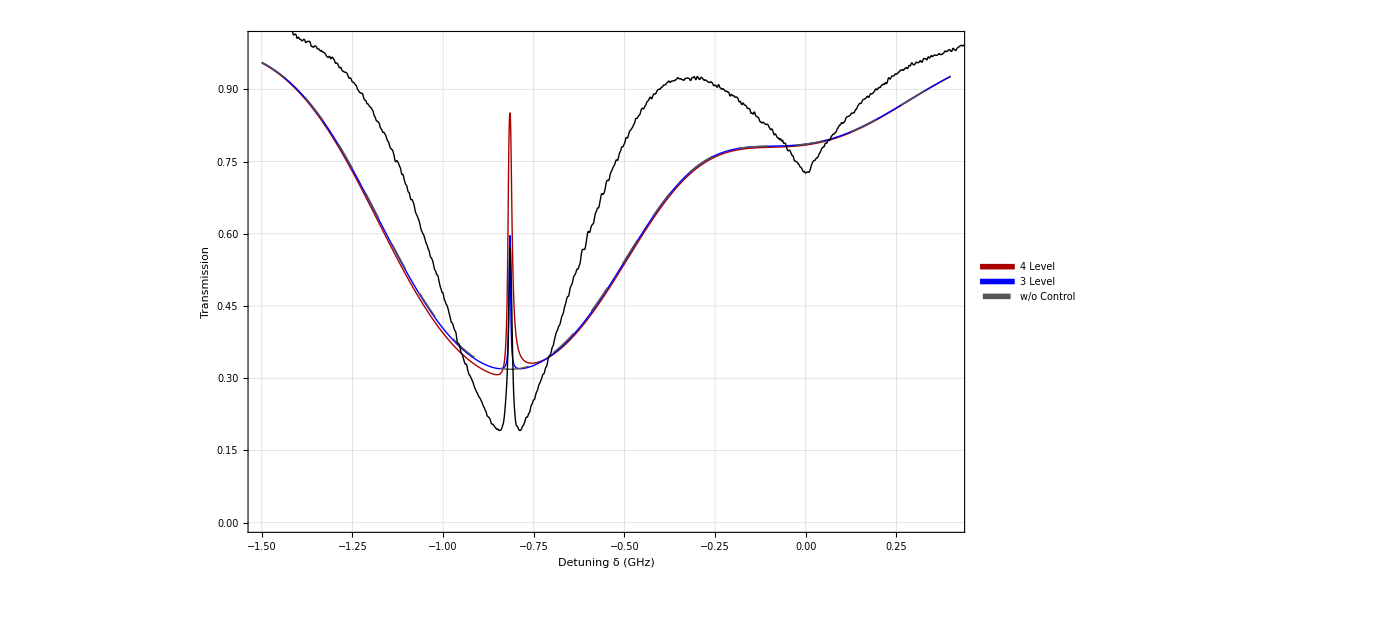

```mathematica
final2=ListPlot[{Lev4DoppTestsc[32,15/1000,0.9/1000,1.438*10^6,-816*10^6,0],Lev3DoppTestsc[32,15/1000,0.9/1000,1.438*10^6,-816*10^6,0],Lev3DoppTestsc[32,0/1000,1/1000,0.5*10^6,0*10^6,0]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,Bottom}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[1],Darker[Red]},{AbsoluteThickness[1],Blue},{AbsoluteThickness[1],Darker[Gray],Dashing[.02]},{AbsoluteThickness[1],Black,Dashed}},FrameLabel->{Style["Detuning δ (GHz)",50,Black],Style["Transmission ",50,Black]},GridLines->Automatic,PlotRange->{{-1.5,0.4},{0.0,1.0}}];
Show[final2,ListPlot[Transpose[f[data2[[45]]][[{4,2}]]],Joined->True,PlotStyle->{Thick,Black},Epilog->Line[{{-2,1},{2,1}}]]]
```

```mathematica
Lev3DoppTestsc[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,Δ2,d31,d41},
d=Range[-1.5,0.4,0.0003]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[1/18]*2.5373 10^-29;
d42=Sqrt[5/18]*2.5373 10^-29;
d31=Sqrt[1/6]*2.5373 10^-29;
d41=Sqrt[1/6]*2.5373 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(816*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 
If[ab==0,
(*{Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}]
}*)Transpose[{d/10^9,
Exp[-2Pi*0.0254*3/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}],

(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}]*)
If[ab==3,
Transpose[{d/10^9,
(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])}],
{
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]])]}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]
}]
}
]]]
```

```mathematica
Lev4DoppTestsc[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Δ2,d31,d41},
d=Range[-1.5,0.4,0.0003]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[1/18]*2.5373 10^-29;
d42=Sqrt[5/18]*2.5373 10^-29;
d31=Sqrt[1/6]*2.5373 10^-29;
d41=Sqrt[1/6]*2.5373 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(816*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

If[ab==0,
(*{Transpose[{d/10^9,Im[sd24[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd23[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}],
Transpose[{d/10^9,Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}]
}*)
Transpose[{d/10^9,
Exp[-2Pi*0.0254*3/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}]

,
(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}]*)
If[ab==3,
{Transpose[{d/10^9,
Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]
}],
Transpose[{d/10^9,
Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]
}]},
{Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]])]
}]}
]]
]
```

```mathematica
Manipulate[ListPlot[Transpose[f[data2[[i]]][[{4,2}]]],PlotRange->{{-0.00,0.04},{0.2,1.05}},Joined->True,Epilog->Line[{{-2,1},{2,1}}]],{{i,2},1,Length[data2],1}]
```

```mathematica
pw={0.5,1,2,3,4,5,6,7,8,9,10,15,20,25,30,35,40,50,60,70,80};power=Flatten[Transpose[{pw,pw,pw,pw}]];
EITmax8711=Table[
If[i<14,
Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.816<#[[1]]<0.04-0.816&][[All,2]]//Max,
Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.816-0.02<#[[1]]<0.05-0.816&][[All,2]]//Max],{i,1,Length[data],1}];
```

```mathematica
EITmin8711=Table[
If[i<14,
Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.816<#[[1]]<0.04-0.816&][[All,2]]//Min,
Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.816-0.02<#[[1]]<0.05-0.816&][[All,2]]//Min],{i,1,Length[data],1}];
```

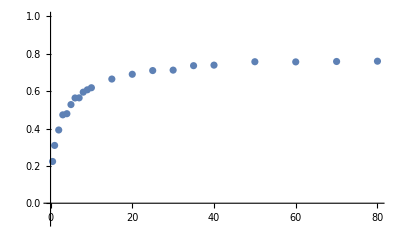

```mathematica
rb8711=ListPlot[{Transpose[{pw,1-Log[Max/@Partition[EITmax8711,4]]/Log[Max/@Partition[EITmin8711,4]]}]},PlotRange->{-0.1,1}]
```

```mathematica
Table[Select[Transpose[f[data2off[[1]]][[{4,2}]]],-0.02<#[[1]]<0.02&][[All,2]]//Min,{i,1,Length[dataoff],1}]//Mean
```

0.396713

```mathematica
halfv8711=EITmin8711+(EITmax8711-EITmin8711)/2
```

{0.322481,0.31935,0.318766,0.318936,0.311389,0.295109,0.319996,0.308412,0.33411,0.304792,0.326323,0.32265,0.343404,0.338248,0.327099,0.32223,0.335107,0.333926,0.329894,0.330729,0.341928,0.339335,0.337571,0.344113,0.353844,0.339364,0.34367,0.351081,0.349459,0.34553,0.348482,0.350861,0.357287,0.356277,0.356057,0.36092,0.358035,0.364228,0.363435,0.356239,0.359397,0.361367,0.367083,0.359378,0.381391,0.382788,0.383474,0.374893,0.392912,0.390891,0.390753,0.388927,0.394926,0.398296,0.400458,0.402113,0.394567,0.401683,0.398078,0.398349,0.413772,0.407634,0.410696,0.40968,0.41423,0.399291,0.417321,0.413507,0.417977,0.424462,0.421341,0.420186,0.426891,0.422794,0.423234,0.423703,0.434711,0.435979,0.432234,0.42468,0.433267,0.43742,0.439377,0.438121}

```mathematica
Manipulate[
Which[i≤4,
ddd=Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.816+0.01<#[[1]]<0.03-0.816&];,
29≥ i>4,
ddd=Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.816<#[[1]]<0.02-0.816&];,
29<i,
ddd=Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.05-0.816<#[[1]]<0.05-0.816&];
];
Nearest[ddd[[All,2]],halfv8711[[i]],4];
pos=Position[ddd[[All,2]],#]&/@Nearest[ddd[[All,2]],halfv8711[[i]],6];
ddd1=ddd[[Sort[Flatten[pos]]]];
f1=Evaluate[Fit[ddd1[[{1,2}]],{1,x},x]];
f2=Evaluate[Fit[ddd1[[{-1,-2}]],{1,x},x]];
Show[ListPlot[{ddd,ddd1},PlotRange->{0,1},PlotStyle->{Black,{Blue,AbsolutePointSize[8]}},Epilog->Line[{{-1,halfv8711[[i]]},{1,halfv8711[[i]]}}]],Plot[{f1,f2},{x,-2,1},PlotRange->{0,1},PlotStyle->{{Red,Dashed},{Red,Dashed}}]]
,{i,1,Length[data2],1}]
Abs[Solve[f1==halfv8711[[1]],x][[1,1,2]]-Solve[f2==halfv8711[[1]],x][[1,1,2]]]*10^3(*in MHz*)
```

6.68416

Part::partd: Part specification halfv8711⟦14⟧ is longer than depth of object.

Nearest::neard: The default distance function does not give a real numeric distance when applied to the point pair halfv8711⟦14⟧ and 0.456054.

Part::partd: Part specification halfv8711⟦14⟧ is longer than depth of object.

Nearest::neard: The default distance function does not give a real numeric distance when applied to the point pair halfv8711⟦14⟧ and 0.456054.

Nearest::near1: {{}} is neither a list of real points nor a valid list of rules.

Nearest::near1: {} is neither a list of real points nor a valid list of rules.

Part::pkspec1: The expression Nearest[{},{},{{}}] cannot be used as a part specification.

Fit::fitd: First argument {{-0.815583,0.456054},{-0.815167,0.45633},{-0.81475,0.456577},{-0.814334,0.456778},{-0.813917,0.456844},{-0.813501,0.456784},{-0.813084,0.456983},{-0.812668,0.457231},{-0.812251,0.457391},«31»,{-0.798922,0.484205},{-0.798505,0.484947},{-0.798089,0.485817},{-0.797672,0.486468},{-0.797256,0.487362},{-0.796839,0.488054},{-0.796423,0.488812},{-0.796006,0.489422}}⟦Nearest[«1»]⟧ in Fit is not a list or a rectangular array.

Part::pkspec1: The expression Nearest[{},{},{{}}] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Fit::fitd: First argument {{-0.815583,0.456054},{-0.815167,0.45633},{-0.81475,0.456577},{-0.814334,0.456778},{-0.813917,0.456844},{-0.813501,0.456784},{-0.813084,0.456983},{-0.812668,0.457231},{-0.812251,0.457391},«31»,{-0.798922,0.484205},{-0.798505,0.484947},{-0.798089,0.485817},{-0.797672,0.486468},{-0.797256,0.487362},{-0.796839,0.488054},{-0.796423,0.488812},{-0.796006,0.489422}}⟦Nearest[«1»]⟧ in Fit is not a list or a rectangular array.

General::stop: Further output of Fit::fitd will be suppressed during this calculation.

Part::partd: Part specification halfv8711⟦14⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

General::ivar: -1.99994 is not a valid variable.

General::ivar: -1.93871 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

```mathematica
width8711=Table[
Which[i≤4,
ddd=Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.816+0.01<#[[1]]<0.03-0.816&];,
29≥ i>4,
ddd=Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.816<#[[1]]<0.02-0.816&];,
29<i,
ddd=Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.05-0.816<#[[1]]<0.05-0.816&];
];
Nearest[ddd[[All,2]],halfv8711[[i]],4];
pos=Position[ddd[[All,2]],#]&/@Nearest[ddd[[All,2]],halfv8711[[i]],6];
ddd1=ddd[[Sort[Flatten[pos]]]];
f1=Evaluate[Fit[ddd1[[{1,2}]],{1,x},x]];
f2=Evaluate[Fit[ddd1[[{-1,-2}]],{1,x},x]];
{power[[i]],Abs[Solve[f1==halfv8711[[1]],x][[1,1,2]]-Solve[f2==halfv8711[[1]],x][[1,1,2]]]*10^3}
,{i,1,Length[data2],1}]
```

{{0.5,5.18607},{0.5,6.26287},{0.5,5.29421},{0.5,5.83746},{1,5.95443},{1,2.00861},{1,6.64142},{1,5.23685},{2,8.58834},{2,4.65617},{2,7.32281},{2,8.03668},{3,9.44802},{3,10.3713},{3,8.21917},{3,7.52533},{4,9.63025},{4,8.74067},{4,8.52403},{4,9.34532},{5,10.1495},{5,9.89418},{5,9.34211},{5,11.3542},{6,12.548},{6,10.1878},{6,10.0792},{6,11.5087},{7,11.5275},{7,10.6521},{7,10.2312},{7,10.6896},{8,11.4108},{8,11.9361},{8,11.1839},{8,11.7164},{9,12.0455},{9,13.0438},{9,13.1624},{9,12.6131},{10,12.183},{10,12.5015},{10,10.2801},{10,11.1109},{15,14.7272},{15,16.327},{15,16.532},{15,13.5528},{20,18.9971},{20,18.2297},{20,18.8762},{20,19.1708},{25,19.3482},{25,22.5642},{25,20.0083},{25,20.6819},{30,19.8075},{30,22.5713},{30,21.5081},{30,23.9042},{35,26.5596},{35,25.0902},{35,24.9366},{35,25.1066},{40,26.1668},{40,4452.31},{40,29.7533},{40,27.1521},{50,34.2113},{50,31.6762},{50,33.3278},{50,33.2889},{60,34.7272},{60,35.6189},{60,34.1447},{60,35.6105},{70,39.5165},{70,39.3169},{70,42.9834},{70,40.4772},{80,45.4897},{80,44.1069},{80,42.8001},{80,44.0877}}

```mathematica
rb87w11={{0.5,5.186069174774377},{0.5,6.262874359875603},{0.5,5.294208644293974},{0.5,5.8374624243408},{1,5.954427557478437},{1,2.008610726084048},{1,6.641424477430102},{1,5.2368512355016605},{2,8.58834252274876},{2,4.656170529085291},{2,7.3228137754496325},{2,8.036677250428227},{3,9.448022590981653},{3,10.371290558736423},{3,8.219170061529946},{3,7.5253334557366935},{4,9.630253621910612},{4,8.740665080841815},{4,8.524025131039782},{4,9.345324153385736},{5,10.149520127148758},{5,9.894175203634115},{5,9.342111785353268},{5,11.354231494030254},{6,12.547973590202655},{6,10.187792393942852},{6,10.079183052321806},{6,11.508700016796048},{7,11.527483260173943},{7,10.65205556237736},{7,10.231155840828233},{7,10.689644162682143},{8,11.410807118257926},{8,11.936126076672714},{8,11.183894110137317},{8,11.71639224492349},{9,12.045484364391012},{9,13.043791339119704},{9,13.162352007189625},{9,12.61312274929316},{10,12.182960506617269},{10,12.501509710895476},{10,10.280080136415348},{10,11.110922510105814},{15,14.727160964238761},{15,16.326989440951678},{15,16.53202909387108},{15,13.552810258794956},{20,18.99711630644907},{20,18.22972182924676},{20,18.876173633550096},{20,19.17076349552016},{25,19.34824318900874},{25,22.56419224992312},{25,20.008290058977863},{25,20.68191490070481},{30,19.807484375306327},{30,22.571313865712206},{30,21.508080046077072},{30,23.904205774582298},{35,26.559630172771854},{35,25.090214274512302},{35,24.936588290763506},{35,25.10658229261975},{40,26.166811406345026},{40,4452.308125480122},{40,29.753278603370738},{40,27.152053408795783},{50,34.21129728229244},{50,31.676179403385962},{50,33.32782558649316},{50,33.28888359388882},{60,34.72724548269657},{60,35.618874473772436},{60,34.14472874291907},{60,35.61051838401885},{70,39.516513694106024},{70,39.31691302792195},{70,42.98343658630854},{70,40.47724859996726},{80,45.48970947473963},{80,44.10693505577967},{80,42.80012454576298},{80,44.08771903324893}}
```

{{0.5,5.18607},{0.5,6.26287},{0.5,5.29421},{0.5,5.83746},{1,5.95443},{1,2.00861},{1,6.64142},{1,5.23685},{2,8.58834},{2,4.65617},{2,7.32281},{2,8.03668},{3,9.44802},{3,10.3713},{3,8.21917},{3,7.52533},{4,9.63025},{4,8.74067},{4,8.52403},{4,9.34532},{5,10.1495},{5,9.89418},{5,9.34211},{5,11.3542},{6,12.548},{6,10.1878},{6,10.0792},{6,11.5087},{7,11.5275},{7,10.6521},{7,10.2312},{7,10.6896},{8,11.4108},{8,11.9361},{8,11.1839},{8,11.7164},{9,12.0455},{9,13.0438},{9,13.1624},{9,12.6131},{10,12.183},{10,12.5015},{10,10.2801},{10,11.1109},{15,14.7272},{15,16.327},{15,16.532},{15,13.5528},{20,18.9971},{20,18.2297},{20,18.8762},{20,19.1708},{25,19.3482},{25,22.5642},{25,20.0083},{25,20.6819},{30,19.8075},{30,22.5713},{30,21.5081},{30,23.9042},{35,26.5596},{35,25.0902},{35,24.9366},{35,25.1066},{40,26.1668},{40,4452.31},{40,29.7533},{40,27.1521},{50,34.2113},{50,31.6762},{50,33.3278},{50,33.2889},{60,34.7272},{60,35.6189},{60,34.1447},{60,35.6105},{70,39.5165},{70,39.3169},{70,42.9834},{70,40.4772},{80,45.4897},{80,44.1069},{80,42.8001},{80,44.0877}}

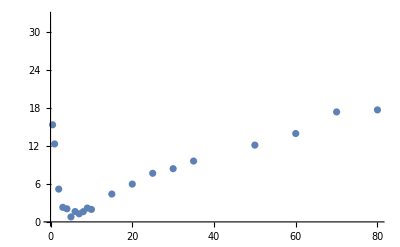

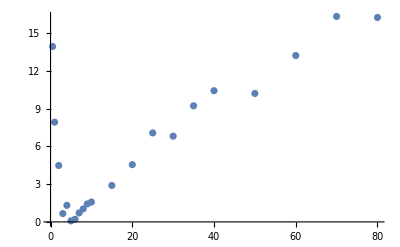

```mathematica
ListPlot[Transpose[{pw,Mean/@Partition[width8711[[All,2]],4]}]]
ListPlot[Transpose[{pw,Min/@Partition[width8711[[All,2]],4]}]]
```

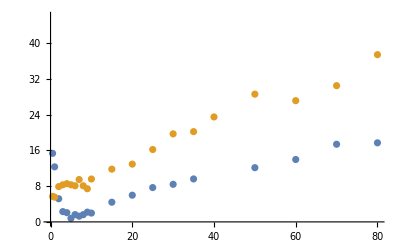

```mathematica
ListPlot[{Transpose[{pw,Mean/@Partition[width8711[[All,2]],4]}],Transpose[{pw,Mean/@Partition[width8511[[All,2]],4]}]}]
```